# Tarea interpolación Lagrange

```mathematica
a = 1; b = 5;
datos = Table[{x,Sin[x]},{x,a,b,1}]
```

{{1,Sin[1]},{2,Sin[2]},{3,Sin[3]},{4,Sin[4]},{5,Sin[5]}}

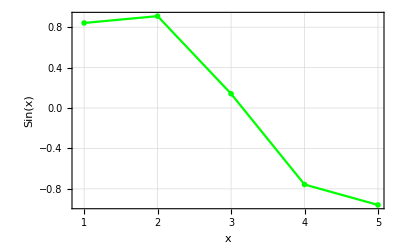

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green}
]
```

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
```

```mathematica
LagrangeBase[datos[[All,1]],0]
```

1/24 (2-x) (3-x) (4-x) (5-x)

```mathematica
Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1/24 (2-x) (3-x) (4-x) (5-x)+1/6 (3-x) (4-x) (5-x) (-1+x)+1/4 (4-x) (5-x) (-2+x) (-1+x)+1/6 (5-x) (-3+x) (-2+x) (-1+x)+1/24 (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
polinomioLagrange=N[LagrangeInterpolate[datos]]
```

-0.649331+2.36813 x-0.9503 x^2+0.0680069 x^3+0.00497029 x^4

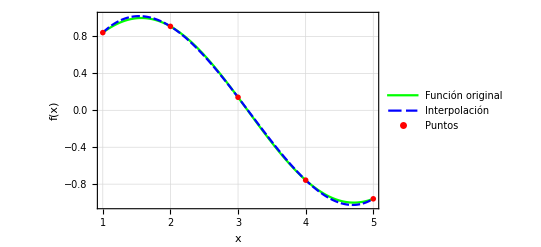

```mathematica
Show[
Plot[
{Sin[x],polinomioLagrange},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

Así vemos que el polinomio obtenido con con la interpolación de Lagrange para sen x con 5 puntos es el mismo obtenido con interpolación polinomial.